```mathematica
PS[n_] := PS[n]= FullSimplify[MangoldtLambda[ n]/Log[n]]
```

```mathematica
DD[n_, k_, a_] :=  DD[n,k,a] = Sum[ PS[j](a^k/k! + DD[n/j, k+1,a]), {j,2,n}]
```

```mathematica
Dd[ n_, a_ ]:= Dd[n,a] = DD[n,1,a]-DD[n-1,1,a]
```

```mathematica
D2[n_,k_] := Sum[ D2[n/j, k-1], {j,2,n}]
```

```mathematica
D2[n_,0] := 1
```

```mathematica
Dd2[ n_, k_] := D2[n,k] - D2[n-1,k]
```

```mathematica
Ds[ n_, k_ ] := Sum[ (-1)^j Binomial[k, k-j] Dd[ n, k-j], {j, 0, 50000 }]
```

```mathematica
Ds[ 8, 2]
```

2

```mathematica
DA[ n_, k_, j_] :=(-1)^j Binomial[k, k-j] Dd[ n, k-j]
DB[ n_, k_, j_] :=  Binomial[k, k-j] Dd[ n, k-j]
DR[ n_, k_ ] := Sum[  Binomial[k, k-j] Dd[ n, k-j], {j, 0, 3000 }]
```

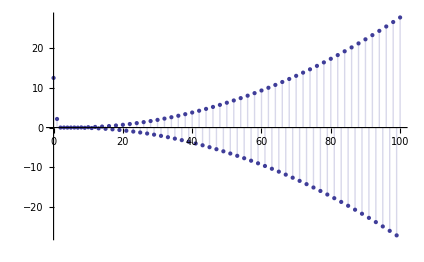

```mathematica
DiscretePlot[DB[72,2.02, j],{j,0, 100,1}]
```

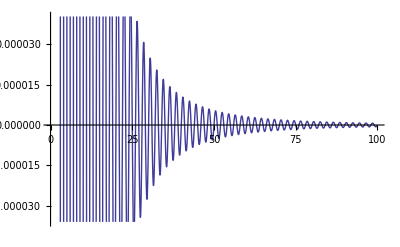

```mathematica
Plot[ Binomial[ 2, 2-x], {x,0,100}]
```

```mathematica
Binomial[4,4-100.1]
```

2.59971×10^-10

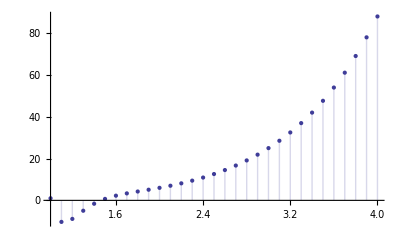

```mathematica
DiscretePlot[DR[8,j],{j,1, 4,.1}]
```